# Progetto di Matematica computazionale

```mathematica
(*Trasforma una stringa nella lista di codici ascii corrispondenti*)
inputString="pipo";
asciiList =ToCharacterCode[inputString]
```

{112,105,112,111}

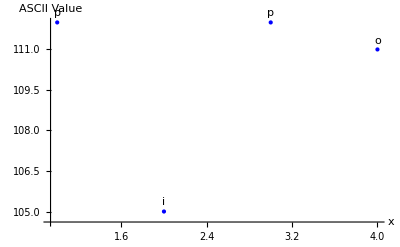

```mathematica
(*Plot original points function*)
points = Transpose[{Range[Length[asciiList]],asciiList}];
charList=Characters[inputString];
labeledPoints=Transpose[{points,charList}];
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
```

155-(205 x)/3+29 x^2-(11 x^3)/3

-205/3+58 x-11 x^2

-1

195-(455 x)/3+(262 x^2)/3-(61 x^3)/3+(5 x^4)/3

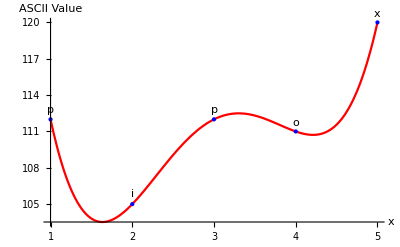

```mathematica
(*Plot polynomial*)
polynomial = Expand[InterpolatingPolynomial[points, x]]
fDev = D[polynomial, x]
fDevSign = Sign[fDev /. x -> asciiList[[-1]]]
If[fDevSign < 0, 
(inputString = inputString <> "x"; asciiList =ToCharacterCode[inputString]; points = Transpose[{Range[Length[asciiList]],asciiList}];charList=Characters[inputString];labeledPoints=Transpose[{points,charList}];labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;polynomial = Expand[InterpolatingPolynomial[points, x]]), 
"all good"]
Show[Plot[polynomial,{x,1,Length[asciiList]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium], Blue}]]
```

```mathematica
(*Error Retrival points*)
maxErrors = 10;
expandedPoints=Table[{i,polynomial/. x->i},{i,Length[points]+maxErrors}];
asciiListExpanded=Round[Last/@expandedPoints];
stringExpanded = FromCharacterCode[asciiListExpanded]
charListExpanded=FromCharacterCode/@asciiListExpanded;
labeledPointsExpanded=Transpose[{expandedPoints,charListExpanded}];
labeledPointsExpandedList=Labeled[#[[1]],#[[2]],Above]&/@labeledPointsExpanded;
```

pipoxÅƸϛߠມᤠ⢇㸨孽舨

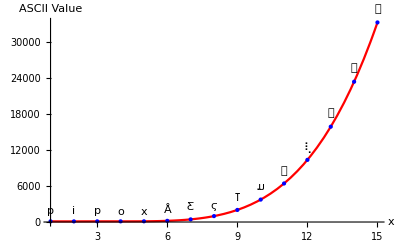

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[polynomial,{x,1,Length[expandedPoints]},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsExpandedList,PlotStyle->{PointSize[Medium],Blue}]]
```

```mathematica
(* String dirter*)
nErrors = RandomInteger[{1,maxErrors}]
errorsPos= RandomSample[Range[StringLength[stringExpanded]],nErrors]

myStringAsList=Characters[stringExpanded];
myStringAsList=Delete[myStringAsList,List/@errorsPos];
corruptedString=StringJoin[myStringAsList]

strLen = StringLength[stringExpanded]
```

10

{13,14,10,1,12,9,6,5,2,4}

pƸϛᤠ舨

15

## ...

```mathematica
(*msg_received =  [corruptedString, errorsPos, strLen, maxErrors];*)
```

```mathematica
asciiList =ToCharacterCode[corruptedString]
charList = Characters[corruptedString];
charsPos=Complement[Range[strLen], errorsPos]
points = Transpose[{charsPos,asciiList}]
labeledPoints=Transpose[{points,charList}]
labeledPointsList=Labeled[#[[1]],#[[2]],Above]&/@labeledPoints;
```

{112,440,987,6432,33320}

{3,7,8,11,15}

{{3,112},{7,440},{8,987},{11,6432},{15,33320}}

{{{3,112},p},{{7,440},Ƹ},{{8,987},ϛ},{{11,6432},ᤠ},{{15,33320},舨}}

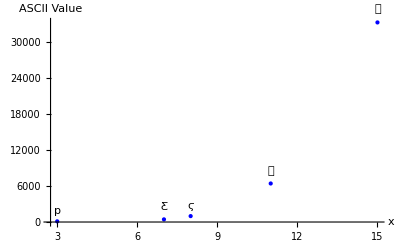

195-(455 x)/3+(262 x^2)/3-(61 x^3)/3+(5 x^4)/3

```mathematica
(*Plot corrupted string points function*)
ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]
reconstructedPoly = Expand[InterpolatingPolynomial[points,x]]
```

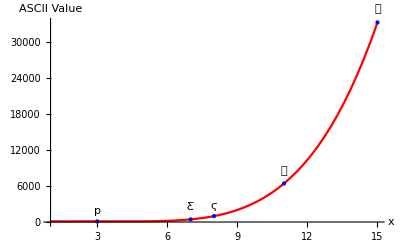

```mathematica
(*Plot polynomial with retriaval error points*)
Show[Plot[reconstructedPoly,{x,1,strLen},PlotStyle->Red,AxesLabel->{"x","ASCII Value"}],ListPlot[labeledPointsList,PlotStyle->{PointSize[Medium],Blue},AxesLabel->{"x","ASCII Value"}]]
```

```mathematica
reconstructedPoints = Table[{i,polynomial/. x->i},{i,strLen-maxErrors}];
reconstructedAsciiList=Round[Last/@reconstructedPoints]
```

{112,105,112,111,120}

```mathematica
reconstructedString = FromCharacterCode[reconstructedAsciiList]
If[fDevSign < 0, StringDrop[reconstructedString, -1], reconstructedString]
```

pipox

pipo